```mathematica
Subscript[K, 1] = 1;
Subscript[K, 3]= 1.32258;
Subscript[e, a]= 11.5;
Subscript[e, 0]=1.42809;
Subscript[e, p]= 7;
γ = Subscript[e, a]/Subscript[e, p];
κ = (Subscript[K, 3]-Subscript[K, 1])/Subscript[K, 1];
V = 1.28996;

F[θ_]:=(2/Pi) √(1+γ (Sin[θ])^2)NIntegrate[√((1+κ(Sin[θ]Sin[λ])^2)/((1+γ(Sin[θ]Sin[λ])^2)(1-(Sin[θ]Sin[λ])^2))),{λ, 0, Pi/2}]-V
```

```mathematica
F[1]
```

0.351904

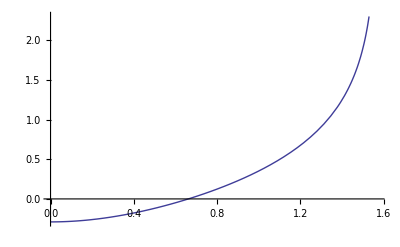

```mathematica
Plot[F[θ], {θ, 0, Pi/2}]
```

```mathematica
M= θ /. FindRoot[F[θ], {θ,.05, 0, Pi/2}, Evaluated->False]
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in λ near {λ} = {1.5707963003801754768168998899441173022761830679883132688701152802}. NIntegrate obtained 13.8794 and 0.448902 for the integral and error estimates.

0.662224

```mathematica
F[M]
```

-2.22045×10^-16

```mathematica
G[ϕ_] := NIntegrate[√((1+κ (Sin[M]Sin[x])^2)(1+γ Sin[M]^2 Sin[x]^2)/(1-Sin[M]^2 Sin[x]^2)),{x, 0, ϕ}]
```

```mathematica
H[y_]:=ϕ /. FindRoot[G[ϕ]-2y NIntegrate[√((1+κ (Sin[M]Sin[x])^2)(1+γ Sin[M]^2 Sin[x]^2)/(1-Sin[M]^2 Sin[x]^2)),{x, 0, Pi/2}],{ϕ, .04, 0, Pi/2}, 
Evaluated->False]
```

```mathematica
J[y_]:= ArcSin[Sin[M]Sin[H[y]]]
```

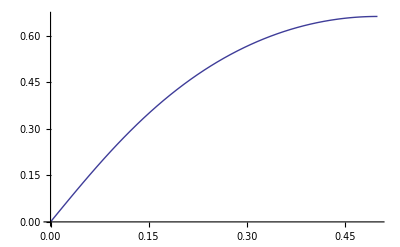

```mathematica
Plot[J[y], {y, 0, .5}]
```

```mathematica
nx[y_] := Cos[J[y]]
ny[y_] :=Sin[J[y]]
```

```mathematica
nx[0.00433949]
```

0.999938